# Asymptotic calculation

## Aim

We have the optimization problem
min σ =F^2/(2D) +∫dx ( p b ln (b/a) + p^B a ln(a/b) )  
	subject to the constraints that
	p^B =1/2 
	∫dx p =1/2
	∫dx a =1
	ℒ = F ∂_x + D ∂_xx - b
	ℒ^* = -F ∂_x + D ∂_xx - b 
	ℒT_1= -1
	ℒT_2 = -2 T_1
	t_2 = ∫dx a T_2
	ℒ^*p + 1/2 a = 0
which can in general only be solved numerically. We wish to derive some asymptotic form in the limit t_2→ ∞, σ → ∞, and to this end we note that numerically simulations show a and b taking the form of sharply peaked functions. We therefore make the simplifying assumption that both a and b take the form of delta functions acting at points x_0 and x_1, and the examine the limit t_2→∞

## Delta function reformulation

We take a = a_0 δ(x-x_0)+a_1 δ(x-x_1), b = b_0 δ(x-x_0)+b_1 δ(x-x_1), so that 
min σ =F^2/(2D) + p(x_0) b_0 ln(b_0/a_0) +p(x_1) b_1 ln(b_1/a_1) +1/2 a_0 ln(a_0/b_0) +1/2 a_1 ln(a_1/b_1) 
	subject to the constraints that
	∫dx p =1/2
	a_0+a_1 =1
	ℒ = F ∂_x + D ∂_xx - b
	ℒ^* = -F ∂_x + D ∂_xx - b 
	ℒT_1= -1
	ℒT_2 = -2 T_1
	t_2 = a_0 T_2(x_0) + a_1 T_2(x_1)
	ℒ^*p + 1/2 a = 0

## Rescaling F and D

We note that the combination F/D appears often so if possible we would wish to replace F/D = l. Replacing a_i →F a_i, b_i→Fb_i, and T_1→ T_1/D, T_2→ T_2/D^2, the problem becomes
min σ =F(l/2 + p(x_0) b_0 ln(b_0/a_0) +p(x_1) b_1 ln(b_1/a_1) +1/2 a_0 ln(a_0/b_0) +1/2 a_1 ln(a_1/b_1) )
	subject to the constraints that
	∫dx p =1/2
	a_0+a_1 =1/F
	ℒ = l ∂_x +  ∂_xx - lb
	ℒ^* = -l ∂_x +  ∂_xx - lb 
	ℒT_1= -1
	ℒT_2 = -2 T_1
	t_2 = l^2/F(a_0 T_2(x_0) + a_1 T_2(x_1))
	ℒ^*p + l/2 a = 0

## Calculation for p

Let us start by calculating p. Away from x_0 and x_1, we have that ℒ^* = -l ∂_x +  ∂_xx, so ℒ^*f = 0 ⇒ f = C_0 + C_1 e^lx . There  will be 2 discontinuities at x_0 and x_1, and different constants for p in the two regions. Let us say that

```mathematica
p1 = C0 + C1 Exp[l x ];
```

```mathematica
p2 = C2 + C3 Exp[l x];
```

Two matching conditions for p1 and p2 come from continuity,
p_1(x_0) = p_2(x_0),
p_1(x_1-1) = p_2(x_1) 
and another 2 conditions come from integrating ℒ^*p + l/2 a = 0 over the the jump,
 ∂_x p_2(x_0) - ∂_x p_1(x_0) - lb_0 p_2(x_0) +l/2 a_0 = 0 
 ∂_x p_1(x_1-1) - ∂_x p_2(x_1) -l b_1 p_2(x_1) +l/2 a_1 = 0

```mathematica
conds={(p1 /. x-> x0) ==(p2 /. x-> x0),(p1 /. x-> (x1-1)) ==(p2 /. x-> x1),
(D[p2,x] /. x-> x0) -  (D[p1,x] /. x-> x0) - l b0 (p2 /. x-> x0) + (l/2) a0 ==0,
 (D[p1,x] /. x-> x1-1) -  (D[p2,x] /. x-> x1) - l b1 (p2 /. x-> x1) + (l/2) a1 ==0,
a0 + a1 == 1/F,
Integrate[p1, {x,x1-1,x0}] + Integrate[p2, {x,x0,x1}] == 1/2};
```

```mathematica
sols = Solve[conds,{C0,C1,C2,C3,a0,a1}]
```

{{C0→(b0 ⅇ^(2 l x0) F+b1 ⅇ^(l x0+l (-1+x1)) F-b0 ⅇ^(l x0+l x1) F-b1 ⅇ^(l (-1+x1)+l x1) F+ⅇ^(l x0+l (-1+x1)) x0-ⅇ^(l x0+l x1) x0-ⅇ^(l x0+l (-1+x1)) x1+ⅇ^(l x0+l x1) x1)/(2 F (b0 ⅇ^(2 l x0)+b1 ⅇ^(l x0+l (-1+x1))-b0 ⅇ^(l x0+l x1)-b1 ⅇ^(l (-1+x1)+l x1)+b0 ⅇ^(l x0+l (-1+x1)) x0+b1 ⅇ^(l x0+l (-1+x1)) x0-b0 ⅇ^(l x0+l x1) x0-b1 ⅇ^(l x0+l x1) x0-b0 ⅇ^(l x0+l (-1+x1)) x1-b1 ⅇ^(l x0+l (-1+x1)) x1+b0 ⅇ^(l x0+l x1) x1+b1 ⅇ^(l x0+l x1) x1)),C1→-((ⅇ^(l x0)-ⅇ^(l x1)) (-1+b0 F+b1 F))/(2 F (b0 ⅇ^(2 l x0)+b1 ⅇ^(l x0+l (-1+x1))-b0 ⅇ^(l x0+l x1)-b1 ⅇ^(l (-1+x1)+l x1)+b0 ⅇ^(l x0+l (-1+x1)) x0+b1 ⅇ^(l x0+l (-1+x1)) x0-b0 ⅇ^(l x0+l x1) x0-b1 ⅇ^(l x0+l x1) x0-b0 ⅇ^(l x0+l (-1+x1)) x1-b1 ⅇ^(l x0+l (-1+x1)) x1+b0 ⅇ^(l x0+l x1) x1+b1 ⅇ^(l x0+l x1) x1)),C2→(ⅇ^(l x0+l (-1+x1))-ⅇ^(l x0+l x1)+b0 ⅇ^(2 l x0) F-b0 ⅇ^(l x0+l (-1+x1)) F+b1 ⅇ^(l x0+l x1) F-b1 ⅇ^(l (-1+x1)+l x1) F+ⅇ^(l x0+l (-1+x1)) x0-ⅇ^(l x0+l x1) x0-ⅇ^(l x0+l (-1+x1)) x1+ⅇ^(l x0+l x1) x1)/(2 F (b0 ⅇ^(2 l x0)+b1 ⅇ^(l x0+l (-1+x1))-b0 ⅇ^(l x0+l x1)-b1 ⅇ^(l (-1+x1)+l x1)+b0 ⅇ^(l x0+l (-1+x1)) x0+b1 ⅇ^(l x0+l (-1+x1)) x0-b0 ⅇ^(l x0+l x1) x0-b1 ⅇ^(l x0+l x1) x0-b0 ⅇ^(l x0+l (-1+x1)) x1-b1 ⅇ^(l x0+l (-1+x1)) x1+b0 ⅇ^(l x0+l x1) x1+b1 ⅇ^(l x0+l x1) x1)),C3→-((ⅇ^(l x0)-ⅇ^(l (-1+x1))) (-1+b0 F+b1 F))/(2 F (b0 ⅇ^(2 l x0)+b1 ⅇ^(l x0+l (-1+x1))-b0 ⅇ^(l x0+l x1)-b1 ⅇ^(l (-1+x1)+l x1)+b0 ⅇ^(l x0+l (-1+x1)) x0+b1 ⅇ^(l x0+l (-1+x1)) x0-b0 ⅇ^(l x0+l x1) x0-b1 ⅇ^(l x0+l x1) x0-b0 ⅇ^(l x0+l (-1+x1)) x1-b1 ⅇ^(l x0+l (-1+x1)) x1+b0 ⅇ^(l x0+l x1) x1+b1 ⅇ^(l x0+l x1) x1)),a0→(b0 ⅇ^(2 l x0)+ⅇ^(l x0+l (-1+x1))-ⅇ^(l x0+l x1)-b0 ⅇ^(l x0+l x1)-b0 b1 ⅇ^(2 l x0) F-b0 ⅇ^(l x0+l (-1+x1)) F-b1 ⅇ^(l x0+l (-1+x1)) F+b0 b1 ⅇ^(l x0+l (-1+x1)) F+b0 ⅇ^(l x0+l x1) F+b1 ⅇ^(l x0+l x1) F+b0 b1 ⅇ^(l x0+l x1) F-b0 b1 ⅇ^(l (-1+x1)+l x1) F+b0 ⅇ^(l x0+l (-1+x1)) x0-b0 ⅇ^(l x0+l x1) x0-b0 ⅇ^(l x0+l (-1+x1)) x1+b0 ⅇ^(l x0+l x1) x1)/(F (b0 ⅇ^(2 l x0)+b1 ⅇ^(l x0+l (-1+x1))-b0 ⅇ^(l x0+l x1)-b1 ⅇ^(l (-1+x1)+l x1)+b0 ⅇ^(l x0+l (-1+x1)) x0+b1 ⅇ^(l x0+l (-1+x1)) x0-b0 ⅇ^(l x0+l x1) x0-b1 ⅇ^(l x0+l x1) x0-b0 ⅇ^(l x0+l (-1+x1)) x1-b1 ⅇ^(l x0+l (-1+x1)) x1+b0 ⅇ^(l x0+l x1) x1+b1 ⅇ^(l x0+l x1) x1)),a1→(-ⅇ^(l x0+l (-1+x1))+b1 ⅇ^(l x0+l (-1+x1))+ⅇ^(l x0+l x1)-b1 ⅇ^(l (-1+x1)+l x1)+b0 b1 ⅇ^(2 l x0) F+b0 ⅇ^(l x0+l (-1+x1)) F+b1 ⅇ^(l x0+l (-1+x1)) F-b0 b1 ⅇ^(l x0+l (-1+x1)) F-b0 ⅇ^(l x0+l x1) F-b1 ⅇ^(l x0+l x1) F-b0 b1 ⅇ^(l x0+l x1) F+b0 b1 ⅇ^(l (-1+x1)+l x1) F+b1 ⅇ^(l x0+l (-1+x1)) x0-b1 ⅇ^(l x0+l x1) x0-b1 ⅇ^(l x0+l (-1+x1)) x1+b1 ⅇ^(l x0+l x1) x1)/(F (b0 ⅇ^(2 l x0)+b1 ⅇ^(l x0+l (-1+x1))-b0 ⅇ^(l x0+l x1)-b1 ⅇ^(l (-1+x1)+l x1)+b0 ⅇ^(l x0+l (-1+x1)) x0+b1 ⅇ^(l x0+l (-1+x1)) x0-b0 ⅇ^(l x0+l x1) x0-b1 ⅇ^(l x0+l x1) x0-b0 ⅇ^(l x0+l (-1+x1)) x1-b1 ⅇ^(l x0+l (-1+x1)) x1+b0 ⅇ^(l x0+l x1) x1+b1 ⅇ^(l x0+l x1) x1))}}

## Calculation of waiting time distribution

Now we have calculated p, we have are able to eliminate a0 and a1. To specify the remaining constraints we must calculate T2 and so first T1. Similar to before, away from x_0 and x_1,  ℒ = l∂_x +  ∂_xx, so ℒf =-1 ⇒ f = -x/l +  C_0 + C_1 e^-lx . There  will be 2 discontinuities at x_0 and x_1, and different constants for T1 in the two regions. Proceeding as before

```mathematica
T1a = - x/l + C4 + C5 Exp[-l x ];
T1b = -x/l + C6 + C7 Exp[-l x ];
```

We can quickly verify these are indeed the general solutions to the ODE:

```mathematica
Simplify[l D[T1a,x] +  D[D[T1a,x],x] + 1]
Simplify[ l D[T1b,x] +  D[D[T1b,x],x] + 1]
```

0

0

Two matching conditions for T1a and T2a come from continuity,
T_(1a)(x_0) = T_(1b)(x_0),
T_(1a)(x_1-1) = T_(1b)(x_1) 
and another 2 conditions come from integrating ℒp  = -1 over the the jump,
 ∂_x T_(1b)(x_0) - ∂_x T_(1a)(x_0) - l b_0 T_(1b)(x_0) = 0 
 ∂_x T_(1a)(x_1-1) - ∂_x T_(1b)(x_1) - l b_1 T_(1b)(x_1) = 0

```mathematica
condsT1={(T1a /. x-> x0) ==(T1b /. x-> x0),(T1a /. x-> (x1-1)) ==(T1b /. x-> x1),
 (D[T1b,x] /. x-> x0) - (D[T1a,x] /. x-> x0) - l b0 (T1b /. x-> x0) ==0,
 (D[T1a,x] /. x-> x1-1) -  (D[T1b,x] /. x-> x1) - l b1 (T1b /. x-> x1)  ==0};
```

```mathematica
solsT1 = Simplify[Solve[condsT1,{C4,C5,C6,C7}]]
```

{{C4→(ⅇ^l (b0 b1 ⅇ^(2 l x0) x0+b0 b1 ⅇ^(l (-1+2 x1)) (-1+x1)-ⅇ^(l (x0+x1)) (1+b0 (1+b1) x0+b1 x1)+ⅇ^(l (-1+x0+x1)) (1+b1 (-1+x1)+b0 (-1+b1+x0-b1 x1))))/((-b0 ⅇ^(l (x0+x1)) (-1+ⅇ^l)-b1 ⅇ^(l (x0+x1)) (-1+ⅇ^l)+b0 b1 (ⅇ^(l x0)-ⅇ^(l x1)) (ⅇ^(l+l x0)-ⅇ^(l x1))) l),C5→(ⅇ^(l (x0+x1)) (-b1 ⅇ^(l x1)+b0 ⅇ^(l x0) (-1+b1 (1+x0-x1))+b0 b1 ⅇ^(l x1) (-1-x0+x1)))/((b0 ⅇ^(l (x0+x1)) (-1+ⅇ^l)+b1 ⅇ^(l (x0+x1)) (-1+ⅇ^l)-b0 b1 (ⅇ^(l x0)-ⅇ^(l x1)) (ⅇ^(l+l x0)-ⅇ^(l x1))) l),C6→(ⅇ^l (b0 b1 ⅇ^(2 l x0) x0+b0 b1 ⅇ^(l (-1+2 x1)) x1+ⅇ^(l (-1+x0+x1)) (1+b0 x0+b1 (-1-b0 x0+x1))-ⅇ^(l (x0+x1)) (1+b1 x1+b0 (1+x0+b1 x1))))/((-b0 ⅇ^(l (x0+x1)) (-1+ⅇ^l)-b1 ⅇ^(l (x0+x1)) (-1+ⅇ^l)+b0 b1 (ⅇ^(l x0)-ⅇ^(l x1)) (ⅇ^(l+l x0)-ⅇ^(l x1))) l),C7→(ⅇ^(l (1+x0+x1)) (-b1 ⅇ^(l (-1+x1))+b0 ⅇ^(l x0) (-1+b1 (x0-x1))+b0 b1 ⅇ^(l (-1+x1)) (-x0+x1)))/((b0 ⅇ^(l (x0+x1)) (-1+ⅇ^l)+b1 ⅇ^(l (x0+x1)) (-1+ⅇ^l)-b0 b1 (ⅇ^(l x0)-ⅇ^(l x1)) (ⅇ^(l+l x0)-ⅇ^(l x1))) l)}}

```mathematica
C7 /. solsT1[[1]] /. plotsubs
```

-0.106132

Now we must essentially repeat the calculation, but for ℒT_2=-2 T_1 . To do so, we use that ℒf =2x/l -2  C_i -2 C_(i+1)e^(-Fx/D)  ⇒ f = x^2/l^2 -(1+2 C_i)x/l+  2 x C_(i+1)/l e^(-Fx/D) +C_k + C_(k+1)e^(-Fx/D) . As before,

```mathematica
T2a = x^2/l^2 - (2/l^2 + 2 C4) x /l + 2 x C5 Exp[-l x ] /l+ C8 + C9 Exp[-l x ];
T2b = x^2/l^2 - (2/l^2 + 2 C6) x /l + 2 x C7 Exp[-l x ] /l+ C10 + C11 Exp[-l x ];
```

Again, quickly verify we have got the correct general solution to the ODE:

```mathematica
Simplify[l D[T2a,x] +  D[D[T2a,x],x] + 2  T1a]
Simplify[ l D[T2b,x] +  D[D[T2b,x],x] + 2  T1b]
```

0

0

```mathematica
condsT2={(T2a /. x-> x0) ==(T2b /. x-> x0),(T2a /. x-> (x1-1)) ==(T2b /. x-> x1),
 (D[T2b,x] /. x-> x0) -  (D[T2a,x] /. x-> x0) - l b0 (T2b /. x-> x0) ==0,
 (D[T2a,x] /. x-> x1-1) -  (D[T2b,x] /. x-> x1) - l b1 (T2b /. x-> x1)  ==0};
```

```mathematica
solsT2 = Simplify[Solve[condsT2,{C8,C9,C10,C11}]]
```

{{C8→(-(-1+ⅇ^l) l (-2 C7 (ⅇ^(l x0)-ⅇ^(l x1))+2 C5 (ⅇ^(l+l x0)-ⅇ^(l x1))+ⅇ^(l (x0+x1)) (1+2 C4 l (1+x0-x1)-2 x1+2 C6 l (-x0+x1)))+b0 (2 C7 ⅇ^(l x0) l-b1 ⅇ^(l+2 l x0) x0 (-2-2 C4 l^2+l x0)+(1+b1) ⅇ^(l (1+x0+x1)) x0 (-2-2 C4 l^2+l x0)-2 C5 ⅇ^(l+l x0) l (1+b1 l (1+x0-x1))-2 C5 ⅇ^(l+l x1) l (-1-(1+b1) l (1+x0-x1))+2 C7 ⅇ^(l x1) l (-1+l (-x0+x1))+ⅇ^(l (x0+x1)) (2 x0+2 l^2 (C6 (x0-x1)+C4 (-1+x1))+l (-1+2 C4-2 C6-x0^2+2 x1)-b1 (-1+x1) (2+l+2 C4 l^2-l x1))+ⅇ^(2 l x1) (-2-2 C4 l+2 C6 l+b1 (-1+x1) (2+l+2 C4 l^2-l x1)))+b1 (2 (C4-C6) ⅇ^(l+2 l x0) l+2 (C5-C7) ⅇ^(l+l x1) l+ⅇ^(l (x0+x1)) (-1+x1) (2+l+2 C4 l^2-l x1)+2 ⅇ^(l+l x0) l (C7+C5 (-1+l (1+x0-x1))+C7 l (-x0+x1))+ⅇ^(l (1+x0+x1)) (-2 C4 l (1+l x0)+2 C6 l (1+l x0-l x1)+x1 (-2+l x1))))/((-b0 ⅇ^(l (x0+x1)) (-1+ⅇ^l)-b1 ⅇ^(l (x0+x1)) (-1+ⅇ^l)+b0 b1 (ⅇ^(l x0)-ⅇ^(l x1)) (ⅇ^(l+l x0)-ⅇ^(l x1))) l^3),C9→(b1 (2 (C5-C7) ⅇ^(2 l x1) l+2 (C4-C6) ⅇ^(l (2 x0+x1)) l-2 C5 ⅇ^(l (1+x0+x1)) l^2 (-1+x1)+2 ⅇ^(l (x0+x1)) l (C7+C5 (-1+l x0)+C7 l (-x0+x1))+ⅇ^(l (x0+2 x1)) (-2+l (-1-2 C4+2 C6+2 x1)-2 l^2 (C4 (1+x0-x1)+C6 (-x0+x1))))-b0 (-2 C7 ⅇ^(2 l x0) l+2 C5 ⅇ^(l+2 l x0) l+2 ⅇ^(l (x0+2 x1)) (1+C4 l-C6 l)+2 ⅇ^(l (x0+x1)) l (C7-C5 l x0+C7 l (x0-x1))+2 C5 ⅇ^(l (1+x0+x1)) l (-1+l (-1+x1))+ⅇ^(l (2 x0+x1)) l (1+2 C4 (-1+l (1+x0-x1))-2 x1+C6 (2-2 l x0+2 l x1))+b1 (-2 C5 ⅇ^(2 l x1) l^2 x0+2 C5 ⅇ^(l (x0+x1)) l^2 x0-2 C5 ⅇ^(l+2 l x0) l^2 (-1+x1)+2 C5 ⅇ^(l (1+x0+x1)) l^2 (-1+x1)+ⅇ^(l (x0+2 x1)) (1+x0-x1) (2+2 C4 l^2-l (-1+x0+x1))+ⅇ^(l (2 x0+x1)) (1+x0-x1) (-2-2 C4 l^2+l (-1+x0+x1)))))/((b0 ⅇ^(l (x0+x1)) (-1+ⅇ^l)+b1 ⅇ^(l (x0+x1)) (-1+ⅇ^l)-b0 b1 (ⅇ^(l x0)-ⅇ^(l x1)) (ⅇ^(l+l x0)-ⅇ^(l x1))) l^3),C10→(-(-1+ⅇ^l) l (-2 C7 (ⅇ^(l x0)-ⅇ^(l x1))+2 C5 (ⅇ^(l+l x0)-ⅇ^(l x1))+ⅇ^(l (x0+x1)) (1+2 C4 l (1+x0-x1)-2 x1+2 C6 l (-x0+x1)))+b0 (-2 C5 ⅇ^(l (2+x0)) l-b1 ⅇ^(l+2 l x0) x0 (-2-2 C6 l^2+l x0)+(-1+b1) ⅇ^(l (x0+x1)) x0 (-2-2 C6 l^2+l x0)-2 C7 ⅇ^(l x1) l (1-(-1+b1) l (x0-x1))-2 C7 ⅇ^(l+l x0) l (-1+b1 l (x0-x1))-2 C5 ⅇ^(l+l x1) l (-1+l (-1-x0+x1))+ⅇ^(2 l x1) (-2-2 C4 l+2 b1 x1-b1 l x1^2+2 C6 l (1+b1 l x1))+ⅇ^(l (1+x0+x1)) (-2 (x0+b1 x1)-2 l^2 (C4 (1+x0-x1)+(1+b1) C6 x1)+l (-1+2 C4-2 C6+x0^2+2 x1+b1 x1^2)))+b1 (2 (C4-C6) ⅇ^(l+2 l x0) l+2 (C5-C7) ⅇ^(l x1) l+ⅇ^(l (1+x0+x1)) x1 (-2-2 C6 l^2+l x1)+2 ⅇ^(l+l x0) l (C7+C5 (-1+l (1+x0-x1))+C7 l (-x0+x1))+ⅇ^(l (x0+x1)) (-l (2 C4-2 C6+(-1+x1)^2)+2 (-1+x1)+2 l^2 (C6 x0+C4 (-1-x0+x1)))))/((-b0 ⅇ^(l (x0+x1)) (-1+ⅇ^l)-b1 ⅇ^(l (x0+x1)) (-1+ⅇ^l)+b0 b1 (ⅇ^(l x0)-ⅇ^(l x1)) (ⅇ^(l+l x0)-ⅇ^(l x1))) l^3),C11→(b1 (2 (C5-C7) ⅇ^(2 l x1) l+2 (C4-C6) ⅇ^(l (1+2 x0+x1)) l+2 ⅇ^(l (1+x0+x1)) l (C7-C7 l x0+C5 (-1+l (1+x0-x1)))+2 C7 ⅇ^(l (x0+x1)) l^2 x1+ⅇ^(l (x0+2 x1)) (-2+l (-1-2 C4+2 C6+2 x1)-2 l^2 (C4 (1+x0-x1)+C6 (-x0+x1))))+b0 (-2 C5 ⅇ^(2 l (1+x0)) l+2 b1 C7 ⅇ^(2 l x1) l^2 x0+2 ⅇ^(l (1+x0+x1)) l (C5-(1+b1) C7 l x0+C5 l (1+x0-x1))-2 C7 ⅇ^(l (x0+x1)) l (1+(-1+b1) l x1)+2 C7 ⅇ^(l+2 l x0) l (1+b1 l x1)+ⅇ^(l (1+2 x0+x1)) (-2 l^2 (-(1+b1) C6 (x0-x1)+C4 (1+x0-x1))+2 b1 (x0-x1)+l (-1+2 C4-2 C6-b1 x0^2+2 x1+b1 x1^2))+ⅇ^(l (x0+2 x1)) (-2-2 C4 l-2 b1 x0+b1 l x0^2+2 b1 x1-b1 l x1^2+2 C6 l (1+b1 l (-x0+x1)))))/((b0 ⅇ^(l (x0+x1)) (-1+ⅇ^l)+b1 ⅇ^(l (x0+x1)) (-1+ⅇ^l)-b0 b1 (ⅇ^(l x0)-ⅇ^(l x1)) (ⅇ^(l+l x0)-ⅇ^(l x1))) l^3)}}

## Final expression

We are now finally in a position where we have eliminated all of the constraints, except for the constraint on t2. We have that

```mathematica
sig = F(l/2 + (p2 /. x->x0) b0 Log[b0/a0] + (p2 /. x->x1) b1 Log[b1/a1] + (a0 Log[a0/b0] + a1 Log[a1/b1] )/2 );
t2 = l^2/F( a0 (T2b /. x-> x0) + a1 (T2b /. x-> x1));
```

We can substitute in values which we have already eliminated to leave these as functions of x_0,x_1,b_0,b_1,F,D

```mathematica
sig = sig /. sols[[1]];
t2 = t2 /. solsT2 /. solsT1/. sols;
```

```mathematica
p2 = p2 /. sols[[1]];
p1 = p1 /. sols[[1]];
```

The resulting expressions are sufficiently complex that they can only be understood by plotting or by using Mathematica’s functions for asymptotic analysis.

## Visualizing solutions

We can now check what the various functions we have found look like for a concrete set of parameter values, which can be easily adjusted

```mathematica
plotsubs =  {x0-> 0.0, x1 -> 0.9, b0 -> 0.15, b1 -> 0.8, F -> 1.25, l -> 6};
```

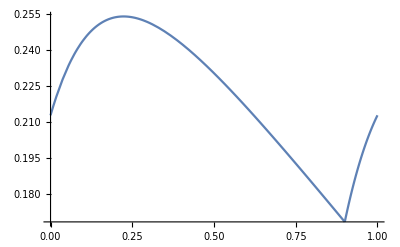

```mathematica
plt1 = Plot[Evaluate[T1b/. solsT1[[1]]/.plotsubs],{x,x0 /. plotsubs,x1 /. plotsubs}];
plt2 = Plot[Evaluate[T1a/. solsT1[[1]]/.plotsubs  /. x-> x-1],{x,x1 /. plotsubs,1}];
Show[plt1,plt2,PlotRange->All]
```

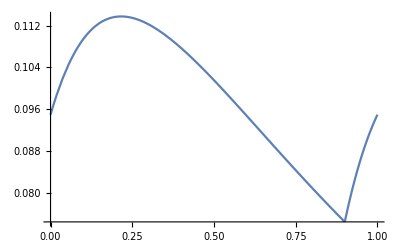

```mathematica
plt1 = Plot[Evaluate[T2b/. solsT2[[1]]/. solsT1[[1]]/.plotsubs],{x,x0 /. plotsubs,x1 /. plotsubs}];
plt2 = Plot[Evaluate[T2a/. solsT2[[1]]/. solsT1[[1]]/.plotsubs/. x-> x-1],{x,x1 /. plotsubs,1}];
Show[plt1,plt2,PlotRange->All]
```

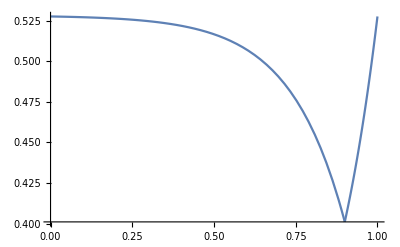

```mathematica
plt1 = Plot[Evaluate[p2/. sols[[1]]/.plotsubs],{x,x0 /. plotsubs,x1 /. plotsubs}];
plt2 = Plot[Evaluate[p1/. sols[[1]]/.plotsubs /. x-> x-1],{x,x1 /. plotsubs,1}];
Show[plt1,plt2,PlotRange->All]
```

## Asymptotic analysis

We could choose a set of values for x_1, F, l, b_0,b_1, (wlog x_0=0), and compute numerically σ and t_2, or numerically minimize over those parameters holding t_2fixed. However, here we derive an analytic expression for the entropy production in the limit that t_2→1. To get t_2=1 exactly, requires a trajectory to enter at x_0, (so a_1 = 0) proceed deterministically (so l = ∞), at velocity F= x_1, before leaving at x_1 (b_0=0, b_1=∞). This will provide intuition for the size of terms of the  t_2→1 limit. To start, let us take x_1=3/4 and find the optimal asymptotics, after which we will show that the choice of x_1 is arbitrary.

```mathematica
asympSubs = {x0-> 0, F->3/4,x1 -> 3/4 } ;
```

```mathematica
t2lim =1+ Simplify[Assuming[{b0 >= 0,b1>0},Asymptotic[(t2 -1)/. asympSubs, l->Infinity]]][[1]][[1]][[1]]
```

1-(2 (-6 b0+14 b1+b0^2 (1+b1)))/(3 (b0-3 b1) (b0+b1+b0 b1))

This asymptotic form assumes b_0 and b_1 are finite in the limit. However, we know b_0→ 0, b_1→∞. In this case we get (here we take b_1 = O(l^2), b_2 = O(e^-l)  as an example)

```mathematica
asympSubs = {x0-> 0, F->3/4,x1 -> 3/4 ,b0 -> A Exp[-l], b1 -> B l^2 } ;
```

```mathematica
t2lim = 1+ Simplify[Assuming[{B>0,A>0},Asymptotic[(t2 -1)/. asympSubs, l->Infinity]]][[1]][[1]][[1]]
```

1+8/(3 l)

If we perturb F around its default value, we find

```mathematica
asympSubs = {x0-> 0, F->3/4+Fp,x1 -> 3/4,b0 -> A Exp[-l],  b1 -> B l^2 } ;
t2lim = 1+ Simplify[Assuming[{Fp ∈ Reals,B>0,A>0},Asymptotic[t2 -1/. asympSubs, l->Infinity]]][[1]][[1]][[1]]
```

1-(4 Fp)/(3+4 Fp)

We know we can’t do better than t_2=1, so what goes wrong with this expression? If we check the value of a_0 under this scaling, we find that

```mathematica
asympSubs = {x0-> 0, F->3/4+Fp,x1 -> 3/4 };
```

```mathematica
a1lim = Simplify[PowerExpand[Assuming[{A > 0,B>0},Asymptotic[ a1  /. sols[[1]] /.  asympSubs/. l -> Log[s],s->Infinity]/. s-> Exp[l]]]]
```

ConditionalExpression[(4 (-4+4 b1 Fp+b0 (1+b1) (3+4 Fp)))/((b0-3 b1) (3+4 Fp)), (1/(3/4+Fp)|b0|b1|b0 b1 (3/4+Fp)|Fp)∈ℝ]

which is only positive (as required), so long as (4 F_p + 3 b_0)b_1 < 1 in the limit. We also know that F_p must be at least as small as O(1/l) as t_2>1 always holds, so 8/(3l)-(4 F_p)/3>0 in the limit. For now, let us take F_p = A/l, b_0=C/l, b_1 = B l, so that if A,B,C are O(1), all terms will contribute at the same order for t_2, in which case we find

```mathematica
asympSubs = {x0-> 0, F->3/4+A/l,x1 -> 3/4 ,b1-> B l, b0-> C /l} ;
t2lim = 1+ Simplify[Assuming[{A>0,C>0,B>0},Asymptotic[t2 -1- 4(7 - 3(-2 + A) B)/(9 B l)/. asympSubs, l->Infinity]]][[1]][[1]][[1]]
```

1+(4 (-48+12 A^2 B-8 A (4+3 B)-3 (7+12 B) C))/(27 B l^2)

We check now that the positivity constraints on a_0, a_1 have not been violated

```mathematica
a1lim = PowerExpand[Assuming[{A > 0,C>0,B>0},Asymptotic[ a1  /. sols[[1]] /.  asympSubs/. l -> Log[s],s->Infinity]/. s-> Exp[l]]]
a0lim = Assuming[{A > 0,B>0,C>0},Asymptotic[ a0  /. sols[[1]] /.  asympSubs/. l -> Log[s],s->Infinity]/. s-> Exp[l]]
```

-(16 A)/(9 l)+16/(9 B l)-(4 C)/(3 l)

4/3

We see that the constraints hold provided that 4/(3B) - C - 4/3 A > 0, or (4A+3C)B < 4 Let us now examine the form of σ in the limit:

```mathematica
pb0lim =PowerExpand[Simplify[Assuming[{A > 0,C>0,B>0}, Asymptotic[ (p2 /. x->x0) b0    /. sols[[1]] /.  asympSubs /. l -> Log[s],s->Infinity] /. s-> Exp[l]]]];
pb1lim = Assuming[{A > 0,B>0,C>0}, Asymptotic[ (p2 /. x->x1) b1    /. sols[[1]] /.  asympSubs,l->Infinity]];
sigAsym =F ( l/2 + (pb0lim -a0lim) Log[ b0 / a0lim] + (pb1lim -a1lim)Log[ b1/ a1lim]  ) /. asympSubs
```

(3/4+A/l) (l/2+(-4/3+(2 C)/(3 l)) Log[(3 C)/(4 l)]+(2/3+(16 A)/(9 l)-16/(9 B l)+(4 C)/(3 l)) Log[(B l)/(-(16 A)/(9 l)+16/(9 B l)-(4 C)/(3 l))])

So in the limit, we have σ = (3l)/8 at leading order. The leading order asymptotics are then t_2 = 1 + (7 - 3(-2 +A) B)/(6B σ) where we can now optimize over the parameters so long as  (4A + 3C)B < 4. For any fixed value of B, it will always be advantageous to increase A as much as possible. For that reason, we set C = 0 and AB = 1 (we will return to check these asymptotics). Then we must minimize (2+3 B)/(3B) = 1 + 2/(3B) which occurs when B → ∞, so t_2 = 1+ 1/σ. Technically this has violated our asymptotic assumptions ((4A + 3C)B = 4 in this limit). However, we can achieve this scaling by taking, for example

```mathematica
asympSubs = {x0-> 0, F->3/4+A/l^2 - 1/l^3,x1 -> 3/4 ,b1->   l^2/A , b0-> C /l^4} ;
```

```mathematica
a1lim = PowerExpand[Assuming[{A > 0,C>0,B>0},Asymptotic[ a1  /. sols[[1]] /.  asympSubs/. l -> Log[s],s->Infinity]/. s-> Exp[l]]]
```

16/(9 l^3)

```mathematica
a0lim = Assuming[{A > 0,B>0,C>0},Asymptotic[ a0  /. sols[[1]] /.  asympSubs/. l -> Log[s],s->Infinity]/. s-> Exp[l]]
```

4/3

```mathematica
t2lim = 1+ Simplify[Assuming[{C >0,B>0,A>0},Asymptotic[t2 -1/. asympSubs, l->Infinity]]][[1]][[1]][[1]]
```

1+8/(3 l)

```mathematica
pb0lim =PowerExpand[Simplify[Assuming[{A > 0,B>0,C>0}, Asymptotic[ (p2 /. x->x0) b0    /. sols[[1]] /.  asympSubs /. l -> Log[s],s->Infinity] /. s-> Exp[l]]]];
pb1lim = Assuming[{A > 0,B>0,C>0}, Asymptotic[ (p2 /. x->x1) b1    /. sols[[1]] /.  asympSubs,l->Infinity]];
```

```mathematica
sigAsym =F ( l/2 + (pb0lim -a0lim) Log[ b0 / a0lim] + (pb1lim -a1lim)Log[ b1/ a1lim]  ) /. asympSubs
```

(3/4-1/l^3+A/l^2) (l/2+(-4/3+(2 C)/(3 l^4)) Log[(3 C)/(4 l^4)]+(2/3-16/(9 l^3)) Log[(9 l^5)/(16 A)])

```mathematica
sigAsymSimp = PowerExpand[Simplify[Assuming[{A > 0,B>0,C>0},Asymptotic[sigAsym /. l -> Log[s],s->Infinity]/. s-> Exp[l]]] ]
```

(3 l)/8

```mathematica
Simplify[(t2lim-1)  sigAsymSimp]
```

1

Thus it is possible to achieve a scaling t_2 ~ 1 + 1/σ. However, the choice of powers and coefficients to achieve this was somewhat arbitrary. The above choice will be asymptotically optimal, but we can do better by finding the next term in the asymptotic expansion and choosing powers and coefficients to minimize that. To that end, let us examine formally what happens as B becomes large with AB fixed.

```mathematica
asympSubs = {x0-> 0, F->3/4+1/(B  l) - D/l^2,x1 -> 3/4 ,b1-> B  l, b0-> C/(l^2)} ;
t2lim = 1+ Simplify[Assuming[{C >0,B>0,A>0},Asymptotic[t2 -1/. asympSubs /. x0->0, l->Infinity]]][[1]][[1]][[1]]
```

ConditionalExpression[1+(8 (2+3 B))/(9 B l), D∈ℝ]

We get the asymptotic form from earlier t_2=1 + 8/(3l), with an additional (smaller) correction 16/(9B l). To see how this enters into play, consider the asymptotic form of σ. Note that to have a_1>0, we must have b_0= O(1/l^2) or smaller.

```mathematica
a1lim = Asymptotic[PowerExpand[Assuming[{A > 0,C>0,B>0},Asymptotic[ a1  /. sols[[1]] /.  asympSubs/. l -> Log[s],s->Infinity]/. s-> Exp[l]]],l-> Infinity]
```

ConditionalExpression[-(4 C)/(3 l^2)+(16 D)/(9 l^2), D∈ℝ]

```mathematica
a0lim = Asymptotic[PowerExpand[Assuming[{A > 0,B>0,C>0},Asymptotic[ a0  /. sols[[1]] /.  asympSubs/. l -> Log[s],s->Infinity]/. s-> Exp[l]]],l-> Infinity]
```

ConditionalExpression[4/3, D∈ℝ]

```mathematica
pb0lim =Asymptotic[PowerExpand[Simplify[Assuming[{A > 0,B>0,C>0}, Asymptotic[ (p2 /. x->x0) b0    /. sols[[1]] /.  asympSubs /. l -> Log[s],s->Infinity] /. s-> Exp[l]]]],l->Infinity]
```

ConditionalExpression[(2 C)/(3 l^2), D∈ℝ]

```mathematica
pb1lim = Assuming[{A > 0,B>0,C>0}, Asymptotic[ (p2 /. x->x1) b1    /. sols[[1]] /.  asympSubs,l->Infinity]]
```

ConditionalExpression[2/3, D∈ℝ]

```mathematica
sigAsym =F ( l/2 + (pb0lim -a0lim) Log[ b0 / a0lim] + (pb1lim -a1lim)Log[ b1/ a1lim]  ) /. asympSubs
```

ConditionalExpression[(3/4-D/l^2+1/(B l)) (l/2+(-4/3+(2 C)/(3 l^2)) Log[(3 C)/(4 l^2)]+(2/3+(4 C)/(3 l^2)-(16 D)/(9 l^2)) Log[(B l)/(-(4 C)/(3 l^2)+(16 D)/(9 l^2))]), D∈ℝ]

Any version of this with B→∞ in at most a polynomial way will not contribute to the leading order asymptotics. We can also see that C, D do not contribute to the first two terms of σ, provided (4D)/3-C = O(1). Retaining the first two terms of σ gives that σ = (3l)/8 + 7/2 log l + 1/2 log B + O(1). 
Inverted, this becomes that  l= 8/3 σ-28/3 log σ - 4/3 log B, so that t_2 = 1 + 1/(σ - 7/2 log σ  - 1/2 log B) + 2/(3Bσ) = 1 + 1/σ + (7/2 log σ + 1/2 log B)/σ^2 + 2/(3 B σ) + higher order terms. Minimizing over B finds that B=4/3 σ ~ l/2 , and so
t_2= 1 + 1/σ + (4 log σ)/σ^2. But by taking  B→ ∞,we have violated asymptotic assumptions, and now must check again for consistency with the choice of a 1/l^2log l scaling for b_0:

```mathematica
asympSubs = {x0-> 0, F->3/4+2/ l^2 -D/(l^2 Log[l]),x1 -> 3/4 ,b1->  l^2/2, b0-> C/(l^2 Log[l])} ;
```

```mathematica
t2lim = 1+ 8/3/l + 32/9 /l^2+ Simplify[Assuming[{G >0},Asymptotic[t2 -1- 8/3/l - 32/9/l^2/. asympSubs /. x0->0, l->Infinity]]][[1]][[1]][[1]]
```

ConditionalExpression[1+32/(9 l^2)+8/(3 l)+(4 D)/(3 l^2 Log[l]), (C|D)∈ℝ]

```mathematica
a1lim = Asymptotic[PowerExpand[Assuming[{G>0},Asymptotic[ a1  /. sols[[1]] /.  asympSubs/. l -> Log[s],s->Infinity]/. s-> Exp[l]]],l-> Infinity]
```

ConditionalExpression[-(4 C)/(3 l^2 Log[l])+(16 D)/(9 l^2 Log[l]), (D|C)∈ℝ]

```mathematica
a0lim = Asymptotic[PowerExpand[Assuming[{G > 0},Asymptotic[ a0  /. sols[[1]] /.  asympSubs/. l -> Log[s],s->Infinity]/. s-> Exp[l]]],l-> Infinity]
```

ConditionalExpression[4/3, (D|C)∈ℝ]

```mathematica
pb0lim =Asymptotic[PowerExpand[Simplify[Assuming[{G> 0}, Asymptotic[ (p2 /. x->x0) b0    /. sols[[1]] /.  asympSubs /. l -> Log[s],s->Infinity] /. s-> Exp[l]]]],l->Infinity]
```

ConditionalExpression[(2 C)/(3 l^2 Log[l]), (C|D)∈ℝ]

```mathematica
pb1lim = Simplify[Assuming[{G>0}, Asymptotic[ (p2 /. x->x1) b1    /. sols[[1]] /.  asympSubs,l->Infinity]]]
```

ConditionalExpression[2/3, (D|C)∈ℝ]

```mathematica
sigAsym =F ( l/2 + (pb0lim -a0lim) Log[ b0 / a0lim] + (pb1lim -a1lim)Log[ b1/ a1lim]  ) /. asympSubs
```

ConditionalExpression[(3/4+2/l^2-D/(l^2 Log[l])) (l/2+(2/3+(4 C)/(3 l^2 Log[l])-(16 D)/(9 l^2 Log[l])) Log[l^2/(2 (-(4 C)/(3 l^2 Log[l])+(16 D)/(9 l^2 Log[l])))]+(-4/3+(2 C)/(3 l^2 Log[l])) Log[(3 C)/(4 l^2 Log[l])]), (C|D)∈ℝ&&(D|C)∈ℝ]

So now we have σ = (3l)/8 + 4log l + 3/2 log log l + O(1), which we can check through:

```mathematica
Assuming[{D>0,4D-3C>0},Limit[sigAsym - 3l/8 - 4Log[l] - 3/2Log[ Log[l]] ,l -> Infinity]]
```

ConditionalExpression[-Log[C]-1/2 Log[-(3 C)/2+2 D], (C|D)∈ℝ&&(D|C)∈ℝ]

So σ = (3l)/8 + 4log l + 3/2 log log l +K + o(1) , where K is given above. In particular, this means that l= 8/3[ σ - 4 log σ - 3/2 log logσ - K - 4 log 8/3], hence t_2= 1 + 1/σ +(4 log σ)/σ^2 + O( log log σ / σ^2) , as claimed before. The order of the correction term here may not be optimal, this would be determined by higher order terms in the asymptotics.

## General x_1

Let us now consider what happens if we take x_1!= 3/4,

```mathematica
asympSubs = {x0-> 0, F->x1+A/ l^2 -1/(l^2 Log[l]) ,b1->   B l^2, b0-> 1/(l^2 Log[l])} ;
```

```mathematica
t2lim = Simplify[Assuming[{A∈ Reals,B > 0 , x1 <= 1},Asymptotic[t2 -1/. asympSubs, l->Infinity]]][[1]][[1]][[1]]
```

ConditionalExpression[2/(l x1), x1>1/2]

```mathematica
pb0lim =PowerExpand[Assuming[{A∈ Reals,B > 0,b1>0,x1 <= 1}, Asymptotic[ (p2 /. x->x0) b0    /. sols[[1]] /.  asympSubs /. l -> Log[s],s->Infinity] /. s-> Exp[l]]]
```

ConditionalExpression[1/(2 l^2 x1 Log[l]), x1>1/2]

```mathematica
pb1lim = Simplify[Assuming[{B > 0,x1 ≤ 1}, Asymptotic[ (p2 /. x->x1) b1    /. sols[[1]] /.  asympSubs,l->Infinity]]]
```

ConditionalExpression[1/(2 x1), A∈ℝ&&x1>1/2]

```mathematica
a1lim = PowerExpand[Assuming[{A∈ Reals, B>0,x1 ≤ 1},Asymptotic[ a1  /. sols[[1]] /.  asympSubs/. l -> Log[s],s->Infinity]/. s-> Exp[l]]]
```

ConditionalExpression[-A/(l^2 x1^2)+1/(B l^2 x1^2), x1>1/2]

```mathematica
a0lim = Assuming[{A∈ Reals,B>0,x1 ≤ 1},Asymptotic[ a0  /. sols[[1]] /.  asympSubs/. l -> Log[s],s->Infinity]/. s-> Exp[l]]
```

ConditionalExpression[1/x1, x1>1/2]

```mathematica
sigAsym =F ( l/2 + (pb0lim -a0lim) Log[ b0 / a0lim] + (pb1lim -a1lim)Log[ b1/ a1lim]  ) /.asympSubs
```

ConditionalExpression[(A/l^2+x1-1/(l^2 Log[l])) (l/2+(A/(l^2 x1^2)-1/(B l^2 x1^2)+1/(2 x1)) Log[(B l^2)/(-A/(l^2 x1^2)+1/(B l^2 x1^2))]+(-1/x1+1/(2 l^2 x1 Log[l])) Log[x1/(l^2 Log[l])]), A∈ℝ&&x1>1/2]

```mathematica
Assuming[{A∈ Reals,B > 0,b1>0,x1 <= 1},Asymptotic[sigAsym, l-> Infinity]]
```

ConditionalExpression[(l x1)/2, A∈ℝ&&x1>1/2&&A B<1]

So, to leading order, we get the same asymptotics t_2=1 + 1/σ.  To investigate the next highest order term, note

```mathematica
Simplify[Assuming[{A∈ Reals,B > 0 , x1 <= 1},Asymptotic[t2 -1 - 2/(l x1)/. asympSubs, l->Infinity]]][[1]][[1]][[1]]
```

ConditionalExpression[(1+x1-A B x1)/(B l^2 x1^2), x1>1/2]

As before, we can take AB = 1, so that

```mathematica
asympSubs = {x0-> 0, F->x1+1/ (B l^2) -2/(l^2 Log[l]) ,b1->   B l^2, b0-> 1/(l^2 Log[l])}
```

{x0→0,F→1/(B l^2)+x1-2/(l^2 Log[l]),b1→B l^2,b0→1/(l^2 Log[l])}

```mathematica
Simplify[Assuming[{A∈ Reals,B > 0 , x1 <= 1},Asymptotic[t2 -1 - 2/(l x1)/. asympSubs, l->Infinity]]][[1]][[1]][[1]]
```

ConditionalExpression[1/(B l^2 x1^2), x1>1/2]

```mathematica
pb0lim =PowerExpand[Assuming[{A∈ Reals,B > 0,b1>0,x1 <= 1}, Asymptotic[ (p2 /. x->x0) b0    /. sols[[1]] /.  asympSubs /. l -> Log[s],s->Infinity] /. s-> Exp[l]]]
```

ConditionalExpression[1/(2 l^2 x1 Log[l]), x1>1/2]

```mathematica
pb1lim = Simplify[Assuming[{B > 0,x1 ≤ 1}, Asymptotic[ (p2 /. x->x1) b1    /. sols[[1]] /.  asympSubs,l->Infinity]]]
```

ConditionalExpression[1/(2 x1), x1>1/2]

```mathematica
a0lim = Assuming[{A∈ Reals,B>0,x1 ≤ 1,x1>1/2},Asymptotic[ a0  /. sols[[1]] /.  asympSubs/. l -> Log[s],s->Infinity]/. s-> Exp[l]]
```

1/x1

```mathematica
a1lim = PowerExpand[Assuming[{A∈ Reals, B>0,x1 ≤ 1,x1>1/2},Asymptotic[ a1  /. sols[[1]] /.  asympSubs/. l -> Log[s],s->Infinity]/. s-> Exp[l]]]
```

2/(l^2 x1^2 Log[l])-1/(l^2 x1 Log[l])

```mathematica
sigAsym =F ( l/2 + (pb0lim -a0lim) Log[ b0 / a0lim] + (pb1lim -a1lim)Log[ b1/ a1lim]  ) /.asympSubs
```

ConditionalExpression[(1/(B l^2)+x1-2/(l^2 Log[l])) (l/2+(1/(2 x1)-2/(l^2 x1^2 Log[l])+1/(l^2 x1 Log[l])) Log[(B l^2)/(2/(l^2 x1^2 Log[l])-1/(l^2 x1 Log[l]))]+(-1/x1+1/(2 l^2 x1 Log[l])) Log[x1/(l^2 Log[l])]), x1>1/2]

Which implies that σ = (x_1 l)/2 + 4log l + O(1), and t_2 = 1 + 2/(x_1 l) + O(1/l^2). Combining these in the l → ∞ limit gives that l = 2/x_1 σ - 8/x_1 log σ, so that t_2 = 1 + 1/σ + (4 log σ)/σ^2, as before, insensitive to the choice of x_1.

If we want to check that the above formally converges in the asymptotic sense, we check the following:

```mathematica
obj = F ( l/2 + ((p2 /. x->x0) b0 - a0) Log[b0/a0]  + ((p2 /. x->x1) b1 - a1) Log[b1/a1])   /.sols[[1]] /.asympSubs ;
con = t2[[1]][[1]][[1]] /.asympSubs;
err = (con - (1 + 1/obj +(4 Log[obj])/ ( obj^2 )))/ ( 4Log[obj]/ (2 obj^2 )) ;
```

```mathematica
Limit[err /. x1  -> 0.8,l-> Infinity]
```

ConditionalExpression[0., B>0]

We examine just how fast this convergence is numerically, but here we know that it does converge in the formal asymptotic sense.